```mathematica
u[x_, t_] := (t - .5x) / (1 + (t-.5x)^2)
n = 2
```

2

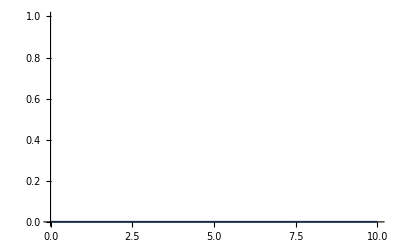
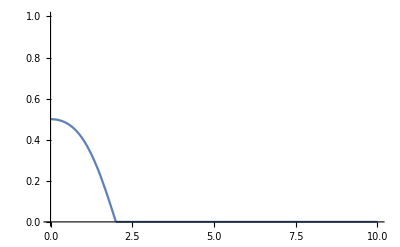
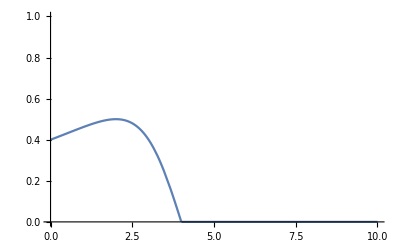
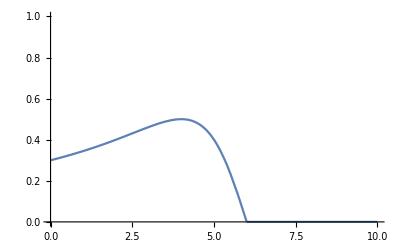

```mathematica
Overlay[{Plot[u[x, 0] Boole[x< 0],{x, 0, 10}, PlotRange->{0, 1}],Plot[u[x, 1] Boole[x< 2(1)],{x, 0, 10},PlotRange->{0, 1}],Plot[u[x, 2] Boole[x< 2(2)],{x, 0, 10}, PlotRange->{0, 1}], 
Plot[u[x, 3] Boole[x< 2(3)],{x, 0, 10}, PlotRange->{0, 1}]}]
```